```mathematica
M=1;
l=Sqrt[12]*M;

V[r_]:=((1/2)×(1-(2M)/r)×(1+(l^2)/(r^2)))-1/2
VEff[r_]:=Sqrt[(1-(2/r))×(1+(l^2)/(r^2))]

rplus=(l^2/(2M))×(1+Sqrt[1-(12×M^2)/(l^2)])
rminus=(l^2/(2M))×(1-Sqrt[1-(12×M^2)/(l^2)])

FullSimplify[V[rplus]]
FullSimplify[V[rminus]]
FullSimplify[VEff[rplus]]
FullSimplify[VEff[rminus]]
```

6

6

-1/18

-1/18

(2 √2)/3

(2 √2)/3

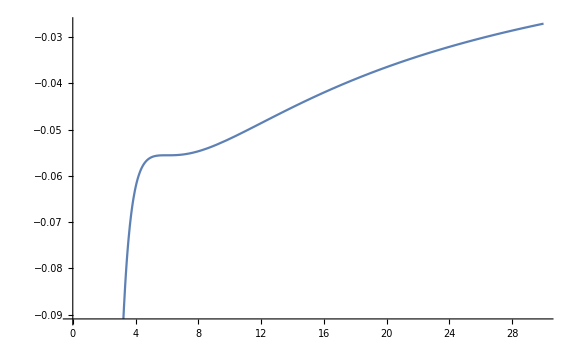

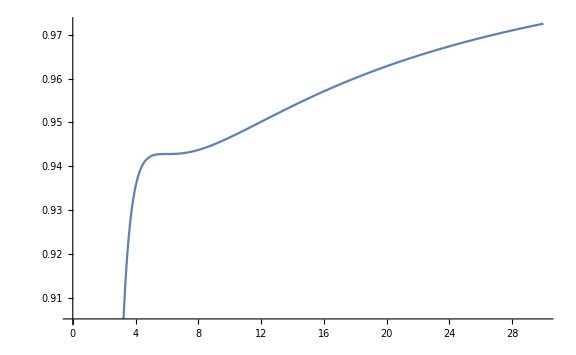

```mathematica
Plot[V[r]/M,{r,0,30}, ImageSize->Large]
Plot[VEff[r]/M,{r,0,30}, ImageSize->Large]
```

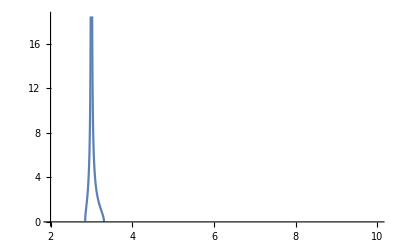

```mathematica
EPerUnitMass[r_]:=((1-(2M)/r)^2)/(1-(3M)/r)
rdot[r_]:=Sqrt[EPerUnitMass[r]^2-1-2×VEff[r]]
Plot[rdot[r],{r,2×M,10×M}]
```